{1,1,1,1,0.01}

{0.4,2,2,2,0.01}

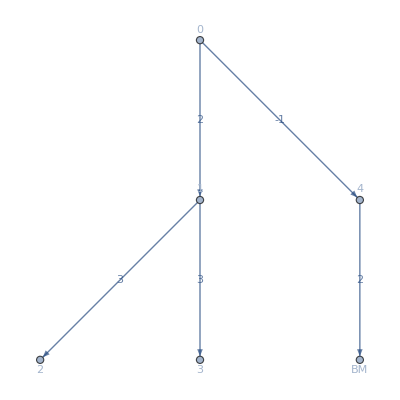

```mathematica
n=5;
Initial[]:=(
in={};
For[j=0,j<n,j++,in=Append[in,Random[]]];
in
);
tmax=800000;

Network={{0,1,2},{1,2,3},{1,3,3},{0,4,-1}};
CataList=Table[Network[[j]][[3]],{j,1,Length[Network],1}];

kLeaker={1,1,1,1,0.01}
kConsumer={0.4,2,2,2,0.01}

Dout=10;
GrowthSym[leaked_,difLeak_,difConsume_,Senv_,Ds_,Rdeg_,Venv_,in1_,in2_]:=(
Dx=Table[0,{i,1,n-1,1}];
Dx[[leaked]]=difLeak;
Dy=Table[0,{i,1,n-1,1}];
Dy[[leaked]]=difConsume;
h=NDSolve[{x[0]'[t]==Ds*(XSenv[t]-x[0][t])-kLeaker[[1]]*x[CataList[[1]]][t]*x[0][t]-kLeaker[[4]]*x[0][t]-x[0][t]*kLeaker[[5]]*x[n-1][t]*x[2][t],
x[1]'[t]==kLeaker[[1]]*x[CataList[[1]]][t]*x[0][t]-kLeaker[[2]]*x[1][t]*x[CataList[[2]]][t]-kLeaker[[3]]*x[1][t]*x[CataList[[3]]][t]+Dx[[1]]*(XM1[t]-x[1][t])-x[1][t]*kLeaker[[5]]*x[n-1][t]*x[2][t],
x[2]'[t]==kLeaker[[2]]*x[1][t]*x[CataList[[2]]][t]-Dx[[2]]*x[2][t]-x[2][t]*kLeaker[[5]]*x[n-1][t]*x[2][t],
x[3]'[t]==kLeaker[[3]]*x[1][t]*x[CataList[[3]]][t]-Dx[[3]]*x[3][t]-x[3][t]*kLeaker[[5]]*x[n-1][t]*x[2][t],
x[4]'[t]==kLeaker[[4]]*x[0][t]-kLeaker[[5]]*x[n-1][t]*x[2][t]-Dx[[4]]*x[4][t]-x[4][t]*kLeaker[[5]]*x[n-1][t]*x[2][t],
px'[t]==(kLeaker[[5]]*x[n-1][t]*x[2][t]-(kLeaker[[5]]*x[n-1][t]*x[2][t]*px[t]+kConsumer[[5]]*y[n-1][t]*y[2][t]*py[t]))*px[t],
y[0]'[t]==Ds*(XSenv[t]-y[0][t])-kConsumer[[1]]*y[CataList[[1]]][t]*y[0][t]-kConsumer[[4]]*y[0][t]-y[0][t]*kConsumer[[5]]*y[n-1][t]*y[2][t],
y[1]'[t]==kConsumer[[1]]*y[CataList[[1]]][t]*y[0][t]-kConsumer[[2]]*y[1][t]*y[CataList[[2]]][t]-kConsumer[[3]]*y[1][t]*y[CataList[[3]]][t]+Dy[[1]]*(XM1[t]-y[1][t])-y[1][t]*kConsumer[[5]]*y[n-1][t]*y[2][t],
y[2]'[t]==kConsumer[[2]]*y[1][t]*y[CataList[[2]]][t]-Dy[[2]]*y[2][t]-y[2][t]*kConsumer[[5]]*y[n-1][t]*y[2][t],
y[3]'[t]==kConsumer[[3]]*y[1][t]*y[CataList[[3]]][t]-Dy[[3]]*y[3][t]-y[3][t]*kConsumer[[5]]*y[n-1][t]*y[2][t],
y[4]'[t]==kConsumer[[4]]*y[0][t]-kConsumer[[5]]*y[n-1][t]*y[2][t]-Dy[[4]]*y[4][t]-y[4][t]*kConsumer[[5]]*y[n-1][t]*y[2][t],
py'[t]==(kConsumer[[5]]*y[n-1][t]*y[2][t]-(kLeaker[[5]]*x[n-1][t]*x[2][t]*px[t]+kConsumer[[5]]*y[n-1][t]*y[2][t]*py[t]))*py[t],
XSenv'[t]==Dout*(Senv-XSenv[t])-Ds*(XSenv[t]-x[0][t])*px[t]/Venv-Ds*(XSenv[t]-y[0][t])*py[t]/Venv-Rdeg*XSenv[t],
XM1'[t]==-Dx[[1]]*(XM1[t]-x[1][t])*px[t]/Venv-Dy[[1]]*(XM1[t]-y[1][t])*py[t]/Venv-Rdeg*XM1[t],
x[0][0]==in1[[1]],x[1][0]==in1[[2]],x[2][0]==in1[[3]],x[3][0]==in1[[4]],x[4][0]==in1[[5]],y[0][0]==in2[[1]],y[1][0]==in2[[2]],y[2][0]==in2[[3]],y[3][0]==in2[[4]],y[4][0]==in2[[5]],px[0]==0.5,py[0]==0.5,XSenv[0]==Senv,XM1[0]==0},{x[0][t],x[1][t],x[2][t],x[3][t],x[4][t],y[0][t],y[1][t],y[2][t],y[3][t],y[4][t],px[t],py[t],XSenv[t],XM1[t]},{t,0,tmax}];
result={x[0][t],x[1][t],x[2][t],x[3][t],x[4][t],y[0][t],y[1][t],y[2][t],y[3][t],y[4][t],XSenv[t],XM1[t]}/.h/.{t->tmax};
mupop={kLeaker[[5]]*x[n-1][t]*x[2][t],kConsumer[[5]]*y[n-1][t]*y[2][t],px[t],py[t]}/.h/.{t->tmax};
{mupop[[1]],result[[1]]}
);


NetworkGraph={};
For[j=1,j≤Length[Network],j++,
n1=Network[[j]][[1]];
n2=Network[[j]][[2]];
n3=Network[[j]][[3]];
NetworkGraph=Append[NetworkGraph,Labeled[n1->n2,ToString[ n3 ] ]] 
];
NetworkGraph=Append[NetworkGraph,Labeled[n-1->BM,2]] ;
Graph[NetworkGraph,VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding"]

k=kLeaker;
k=kConsumer;
GrowthDegV[leaked_,dmore_,Senv_,Ds_,Rdeg_,Vex_,in1_]:=(
Da=Table[0,{i,1,n-1,1}];
Da[[leaked]]=dmore;
h=NDSolve[{x[0]'[t]==Ds*(XSenv[t]-x[0][t])-k[[1]]*x[CataList[[1]]][t]*x[0][t]-k[[4]]*x[0][t]-x[0][t]*k[[5]]*x[n-1][t]*x[2][t],
x[1]'[t]==k[[1]]*x[CataList[[1]]][t]*x[0][t]-k[[2]]*x[1][t]*x[CataList[[2]]][t]-k[[3]]*x[1][t]*x[CataList[[3]]][t]-Da[[1]]*(x[1][t]-XM1[t])-x[1][t]*k[[5]]*x[n-1][t]*x[2][t],
x[2]'[t]==k[[2]]*x[1][t]*x[CataList[[2]]][t]-Da[[2]]*x[2][t]-x[2][t]*k[[5]]*x[n-1][t]*x[2][t],
x[3]'[t]==k[[3]]*x[1][t]*x[CataList[[3]]][t]-Da[[3]]*x[3][t]-x[3][t]*k[[5]]*x[n-1][t]*x[2][t],
x[4]'[t]==k[[4]]*x[0][t]-k[[5]]*x[n-1][t]*x[2][t]-Da[[4]]*x[4][t]-x[4][t]*k[[5]]*x[n-1][t]*x[2][t],
logvx'[t]==k[[5]]*x[n-1][t]*x[2][t],
XSenv'[t]==Dout*(Senv-XSenv[t])-Ds*(XSenv[t]-x[0][t])/Vex-Rdeg*XSenv[t],
XM1'[t]==Da[[1]]*(x[1][t]-XM1[t])/Vex-XM1[t]*Rdeg,
x[0][0]==in1[[1]],x[1][0]==in1[[2]],x[2][0]==in1[[3]],x[3][0]==in1[[4]],x[4][0]==in1[[5]],XSenv[0]==Senv,XM1[0]==0,logvx[0]==0},{x[0][t],x[1][t],x[2][t],x[3][t],x[4][t],XSenv[t],XM1[t],logvx[t]},{t,0,tmax}];
result=Append[Table[x[i][t],{i,0,n-1,1}],XM1[t]]/.h/.{t->tmax};
{k[[5]]*result[[1]][[n]]*result[[1]][[3]],result[[1]]}
);
```

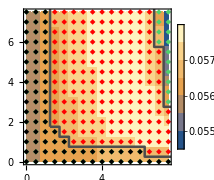

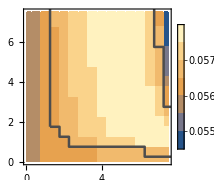

```mathematica
(* Figure 2C*)
μList={};Symbiosis={};nonSymbiosis={};AdvSymbiosis={};nonAdvSym={};
dDif=0.5;
DifMax=7.5;
Co=1;Di=1;Dout=10;deg=1;V=1;

For[DifLeaker=0.0,DifLeaker≤DifMax,DifLeaker+=dDif,
For[DifConsumer=0.0,DifConsumer≤DifMax,DifConsumer+=dDif,
k=kLeaker;
leakerIso=GrowthDegV[1,DifLeaker,Co,Di,deg,V,Initial[]];
k=kConsumer;
consumerIso=GrowthDegV[1,DifConsumer,Co,Di,deg,V,Initial[]];
a=GrowthSym[1,DifLeaker,DifConsumer,Co,Di,deg,V,leakerIso[[2]],consumerIso[[2]]][[1]];
μList=Append[μList,{DifLeaker,DifConsumer,Max[a[[1]],a[[2]]]}];
If[a[[3]]>0.00001&&a[[4]]>0.00001,
Symbiosis=Append[Symbiosis,{DifLeaker,DifConsumer}],
nonSymbiosis=Append[nonSymbiosis,{DifLeaker,DifConsumer}]
];
If[a[[1]]>leakerIso[[1]]&&a[[1]]>consumerIso[[1]],
If[a[[3]]>0.00001&&a[[4]]>0.00001,
AdvSymbiosis=Append[AdvSymbiosis,{DifLeaker,DifConsumer}]
],
nonAdvSym=Append[nonAdvSym,{DifLeaker,DifConsumer}]
];

]
];

Show[ListContourPlot[μList,InterpolationOrder->0,PlotLegends->Automatic],ListPlot[{nonAdvSym,nonSymbiosis,AdvSymbiosis},PlotMarkers->{◆,8},PlotStyle->{Directive[CMYKColor[0.64,0.03,0.5,0.15],PointSize[Medium]],Directive[Black,PointSize[Medium]],Directive[Red,PointSize[Medium]]}],ListLinePlot[{{1.25,1.75},{1.75,1.75},{1.75,1.25},{2.25,1.25},{2.25,1.25},{2.25,0.75},{6.25,0.75},{6.25,0.25},{7.75,0.25}},PlotStyle->{GrayLevel[0.3],Thickness[0.01]},InterpolationOrder->1],ListLinePlot[{{1.25,7.75},{1.25,1.75}},PlotStyle->{GrayLevel[0.3],Thickness[0.01]},InterpolationOrder->1],
ListLinePlot[{{6.75,7.75},{6.75,5.75},{7.25,5.75},{7.25,2.75},{7.75,2.75}},PlotStyle->{GrayLevel[0.3],Thickness[0.01]},InterpolationOrder->1],
FrameTicksStyle->Directive[Black,12],ImageSize->Small]

Show[ListContourPlot[μList,InterpolationOrder->0,PlotLegends->Automatic],ListLinePlot[{{1.25,1.75},{1.75,1.75},{1.75,1.25},{2.25,1.25},{2.25,1.25},{2.25,0.75},{6.25,0.75},{6.25,0.25},{7.75,0.25}},PlotStyle->{GrayLevel[0.3],Thickness[0.01]},InterpolationOrder->1],ListLinePlot[{{1.25,7.75},{1.25,1.75}},PlotStyle->{GrayLevel[0.3],Thickness[0.01]},InterpolationOrder->1],
ListLinePlot[{{6.75,7.75},{6.75,5.75},{7.25,5.75},{7.25,2.75},{7.75,2.75}},PlotStyle->{GrayLevel[0.3],Thickness[0.01]},InterpolationOrder->1],
FrameTicksStyle->Directive[Black,12],ImageSize->Small]
```

{}

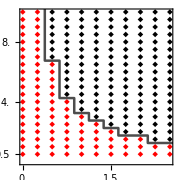

```mathematica
(* Figure 2D *)

μList={};Symbiosis={};nonSymbiosis={};AdvSymbiosis={};nonAdvSym={};
dDeg=0.25;dV=0.5;DifLeaker=4;

For[deg=0,deg≤2.5,deg+=dDeg,
For[V=dV,V≤10,V+=dV,
k=kLeaker;
leakerIso=GrowthDegV[1,DifLeaker,Co,Di,deg,V,Initial[]];
a=GrowthSym[1,DifLeaker,DifLeaker,Co,Di,deg,V,leakerIso[[2]],Initial[]][[1]];
μList=Append[μList,{deg,V,Max[a[[1]],a[[2]]]}];
If[a[[3]]>0.00001&&a[[4]]>0.00001 &&a[[1]]>0.0000001,
Symbiosis=Append[Symbiosis,{deg,V}],
nonSymbiosis=Append[nonSymbiosis,{deg,V}]
];
If[a[[3]]>0.00001&&a[[4]]>0.00001,
If[a[[1]]>leakerIso[[1]],
AdvSymbiosis=Append[AdvSymbiosis,{deg,V}],
nonAdvSym=Append[nonAdvSym,{deg,V}]
]
]
]
];
nonAdvSym
Show[ListPlot[{AdvSymbiosis,nonSymbiosis},PlotMarkers->{◆,8},PlotStyle->{Directive[Red,PointSize[Medium]],Directive[Black,PointSize[Medium]]},AspectRatio->1, Frame->True],
ListLinePlot[{{0.375,10.25},{0.375,6.75},{0.625,6.75},{0.625,4.25},{0.875,4.25},{0.875,3.25},{1.125,3.25},{1.125,2.75},{1.375,2.75},{1.375,2.25},{1.625,2.25},{1.625,1.75},{2.125,1.75},{2.125,1.25},{2.625,1.25}},PlotStyle->{GrayLevel[0.3],Thickness[0.01]},InterpolationOrder->1],
FrameTicks->{{{0.5,2.0,4.0,6.0,8.0,10.0},None},{{0.0,0.5,1.0,1.5,2.0,2.5},None}},FrameTicksStyle->Directive[13],LabelStyle->{GrayLevel[0]},ImageSize->Small]
```